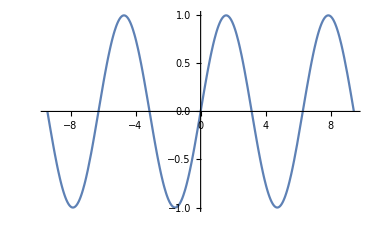

```mathematica
(*Basic Trig Functions Plotting *)

Plot[Sin[x],{x, -3Pi, 3Pi}]
```

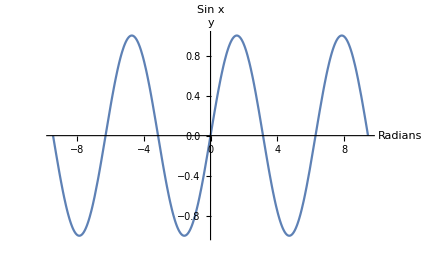

```mathematica
Show[%3,AxesLabel->{HoldForm[Radians],HoldForm[y]},PlotLabel->HoldForm[Sin x],LabelStyle->{FontFamily->"Times New Roman",12,GrayLevel[0],Bold}]
```

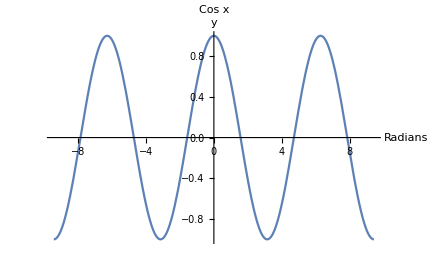

```mathematica
Plot[Cos[x],{x, -3 Pi, 3 Pi}, AxesLabel-> {HoldForm[Radians], HoldForm[y]}, PlotLabel->HoldForm[Cos x], LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0],Bold}]
```

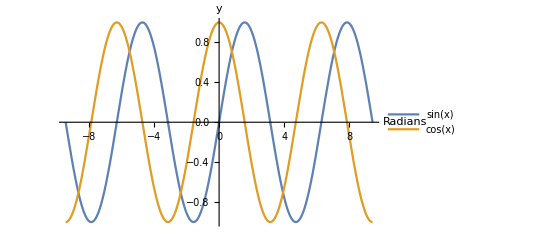

```mathematica
Plot[{Sin[x], Cos[x]},{x, -3 Pi, 3 Pi},PlotLegends->"Expressions", AxesLabel -> {HoldForm[Radians], HoldForm[y]},LabelStyle -> {FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

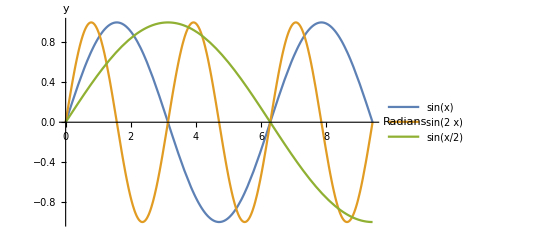

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[x/2]},{x, 0, 3 π}, PlotLegends -> "Expressions", AxesLabel -> {HoldForm[Radians], HoldForm[y]}, LabelStyle -> {FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

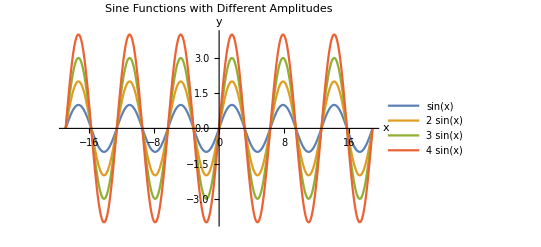

```mathematica
Plot[{Sin[x],2 Sin[x], 3 Sin[x], 4 Sin[x]}, {x, - 6  Pi,6 Pi}, PlotLegends->"Expressions", AxesLabel->{HoldForm[x], HoldForm[y]}, PlotLabel-> HoldForm["Sine Functions with Different Amplitudes"],LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

```mathematica
Clear[a,x]
```

```mathematica
Manipulate[Plot[a Sin[ x],{x,-3 Pi, 3 Pi}],{a, -1, 1}]
```

```mathematica
Manipulate[Plot[a Cos[x],{x, -3 Pi, 3 Pi}], {a, -1, 1}]
```

```mathematica
Animate[Plot[Sin[x+n],{x, 0, 20}],{n,0,10
}, AnimationRunning->False]
```

```mathematica
Animate[Plot[Cos[x + n],{x, 0, 20}], {n, 0, 10}, AnimationRunning->False]
```

```mathematica
FunctionPeriod[Sin[(Pi x)/6],x]
```

12

```mathematica
FunctionPeriod[Cos[x/3],x]
```

6 π

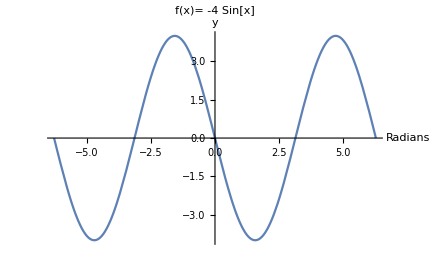

```mathematica
Plot[-4 Sin[x],{x,- 2 Pi, 2 Pi},PlotLabel->"f(x)= -4 Sin[x]",AxesLabel -> {HoldForm[Radians], HoldForm[y]}, LabelStyle -> {FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold} ]
```

```mathematica
FindMaxValue[-4 Sin[x],x](*Finds Amplitude*)
```

4.

```mathematica
FindMaxValue[3/2 Sin[x],x]
```

1.5

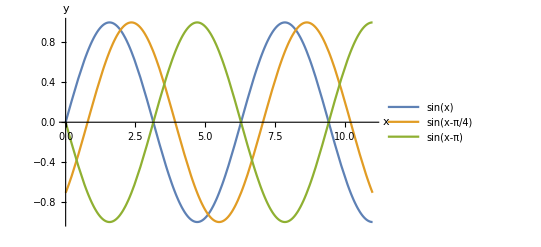

```mathematica
Plot[{Sin[x],Sin[x - (Pi/4)],Sin[x-Pi]},{x, 0, (7 Pi)/2},PlotLegends->"Expressions", AxesLabel->{HoldForm[x], HoldForm[y]},LabelStyle -> {FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

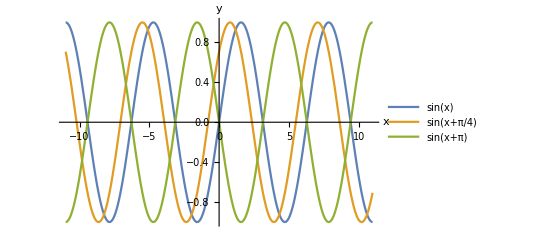

```mathematica
Plot[{Sin[x],Sin[x + (Pi/4)],Sin[x+Pi]},{x, -(7 Pi)/2 ,(7 Pi)/2},PlotLegends->"Expressions", AxesLabel->{HoldForm[x], HoldForm[y]},LabelStyle -> {FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```

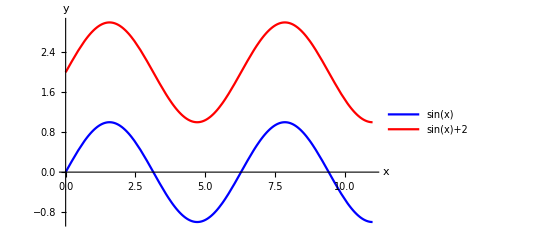

```mathematica
Plot[{Sin[x],Sin[x]+2},{x, 0, (7 Pi)/2},PlotLegends->"Expressions",PlotStyle -> {Blue, Red},AxesLabel->{HoldForm[x],HoldForm[y]},LabelStyle->{FontFamily -> "Times New Roman",12,GrayLevel[0],Bold}]
```

```mathematica
FunctionPeriod[3 Sin[2x]+1,x](* Finding Period *)
```

π

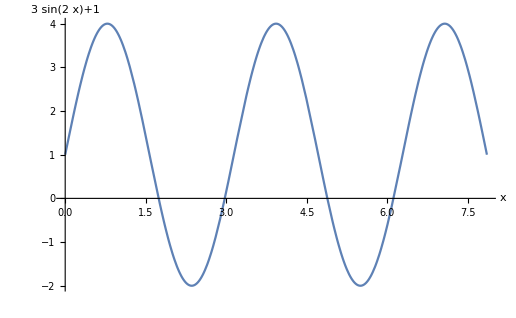

```mathematica
Plot[ 3 Sin[2 x] + 1, {x, 0, (5Pi)/2}, AxesLabel->{HoldForm[x], HoldForm[3 Sin[2 x] + 1]}, LabelStyle->{FontFamily -> "Times New Roman", 12, GrayLevel[0], Bold}]
```